```mathematica
nw=50;
realdata = Import["wmax0.25_Ny15_Nx15_eta0.12_Ns40_ldostotal_with_mg.dat"];
Partition[realdata[[All,1]],12][[1,1]];
```

```mathematica
ldosawithmg=Table[{Partition[realdata[[All,1]],12][[i,1]],Total[Partition[Partition[realdata[[All,2]],12][[i]],6][[1]]]},{i,1,nw+1}];
ldosbwithmg=Table[{Partition[realdata[[All,1]],12][[i,1]],Total[Partition[Partition[realdata[[All,2]],12][[i]],6][[2]]]},{i,1,nw+1}];

realdatawomg = Import["wmax0.25_Ny15_Nx15_eta0.12_Ns40_ldostotal_wo_mg.dat"];

ldosdatwomg=Table[{Partition[realdatawomg[[All,1]],6][[i,1]],Total[Partition[realdatawomg[[All,2]],6][[i]]]},{i,1,nw+1}];
```

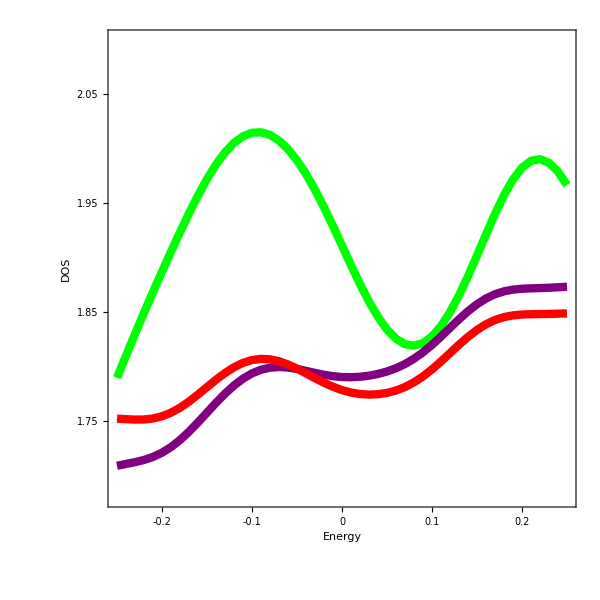

```mathematica
plot=ListPlot[{ldosdatwomg,ldosawithmg,ldosbwithmg},Joined->True,Frame->True,FrameStyle->Directive[Thickness[0.005],Black,45],PlotRange->{{-0.25,0.25},{1.68,2.1}},
FrameTicks->{{{{1.75,1.75,0.03},{1.85,1.85,0.03},{1.95,1.95,0.03},{2.05,2.05,0.03},{2.15,2.15,0.03}},{{1.75,Null,0.03},{1.85,Null,0.03},{1.95,Null,0.03},{2.05,Null,0.03},{2.15,Null,0.03}}},{{{-0.2,-0.2,0.03},{-0.1,-0.1,0.03},{0,0,0.03},{0.1,0.1,0.03},{0.2,0.2,0.03}},{{-0.2,Null,0.03},{-0.1,Null,0.03},{0,Null,0.03},{0.1,Null,0.03},{0.2,Null,0.03}}}},FrameLabel->{{Style["DOS",40,FontFamily->"TimesNewRoman"],""},{Style["Energy",40,FontFamily->"TimesNewRoman"],""}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,25]},PlotStyle->{{Green,Thickness[0.01]},{Purple,Thickness[0.01]},{Red,Thickness[0.01]}},
ImagePadding->{{130,25},{112,15}},Axes->False,ImageSize->600,AspectRatio->1]
Export["plot.eps",plot];
```